## Space Filling Curves

```mathematica
Manipulate[Graphics[c[n]],{n,1,5,1},{c,{HilbertCurve,PeanoCurve,SierpinskiCurve,KochCurve}},ControlType->Automatic]
```

```mathematica
ConvertToRaster[img_]:=EdgeDetect[Binarize[img]]
```

```mathematica
fractalData=<|-Graphics-->0.6309,-Graphics-->1,-Graphics-->1.0812,-Graphics-->1.0933,-Graphics-->1.12915,-Graphics-->1.2,-Graphics-->1.2083,-Graphics-->1.2108,-Graphics-->1.2619,-Graphics-->1.2619,-Graphics-->1.2619,-Graphics-->1.2683,-Graphics-->1.328,-Graphics-->1.3057,-Graphics-->1.3934,-Graphics-->1.4649,-Graphics-->1.4649,-Graphics-->1.5,-Graphics-->1.5,-Graphics-->1.5236,-Graphics-->1.5849,-Graphics-->1.61803,-Graphics-->1.6379,-Graphics-->1.6667,-Graphics-->1.7,-Graphics-->1.7227,-Graphics-->1.7712,-Graphics-->1.7848,-Graphics-->1.8687,-Graphics-->1.8617,-Graphics-->1.8928,-Graphics-->1.974,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->2,-Graphics-->1.9340|>;
```

```mathematica
fractalData=KeyMap[ConvertToRaster,fractalData];
```

```mathematica
fractalData=Normal[fractalData];
```

```mathematica
fractalData=RandomSample[fractalData];
```

```mathematica
training=fractalData[[5;;]];
test=fractalData[[;;4]]
```

{-Graphics-→1.6379,-Graphics-→1.974,-Graphics-→1.5849,-Graphics-→1.2683}

```mathematica
p=Predict[List@@training]
```

PredictorFunction[…]

```mathematica
p/@Keys[test]
```

{1.54831,1.60204,1.72387,1.56543}

```mathematica
JuliaFractalDimension[c_]:=1+Abs[c]^2/4 Log[2]
```

```mathematica
Table[RandomReal[{-1,1}],20]
```

{-0.148923,-0.498341,-0.129607,-0.989846,-0.865903,-0.438573,-0.108611,0.851216,-0.00964472,0.651955,0.756966,0.909146,0.374567,0.797585,-0.677469,0.981197,0.705896,-0.244823,0.375813,-0.230105}

```mathematica
Table[RandomComplex[],20]
```

{0.0191314+0.177534 ⅈ,0.887907+0.918117 ⅈ,0.616259+0.734084 ⅈ,0.675998+0.744802 ⅈ,0.898976+0.959015 ⅈ,0.431962+0.171615 ⅈ,0.352488+0.0453338 ⅈ,0.441151+0.894347 ⅈ,0.186204+0.744615 ⅈ,0.887912+0.454777 ⅈ,0.219896+0.713272 ⅈ,0.71217+0.902298 ⅈ,0.227364+0.85828 ⅈ,0.923437+0.776097 ⅈ,0.402001+0.452464 ⅈ,0.114215+0.866238 ⅈ,0.550196+0.64797 ⅈ,0.938684+0.399923 ⅈ,0.0450352+0.382454 ⅈ,0.227628+0.237972 ⅈ}

```mathematica
CreateJuliaFractals[size_]:=Module[{jFunction={JuliaSetPlot[#],#}&,jFractals},
jFractals=jFunction/@Table[RandomComplex[],Floor[size/2]]∪jFunction/@Table[RandomReal[{-1,1}],Ceiling[size/2]];
#[[1]]->JuliaFractalDimension[#[[2]]]&/@jFractals
]
```

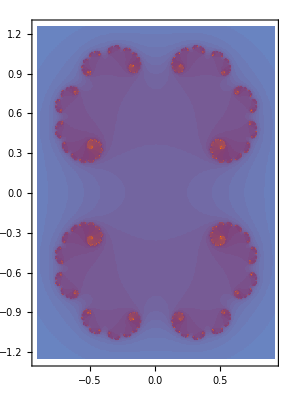
{-Graphics-→1.02379,-Graphics-→1.00504,-Graphics-→1.01358,-Graphics-→1.00034}

```mathematica
CreateJuliaFractals[4]
```

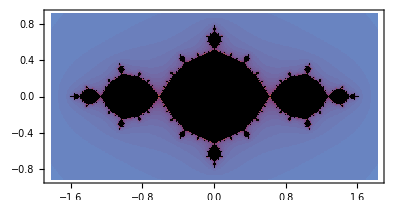
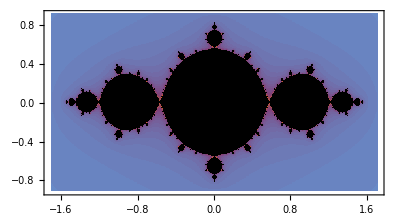
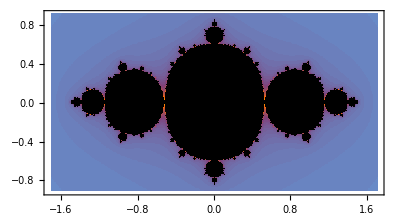
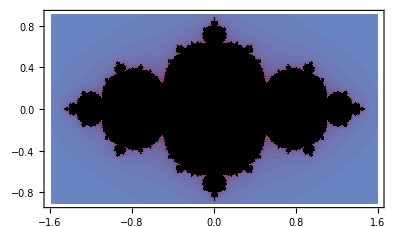
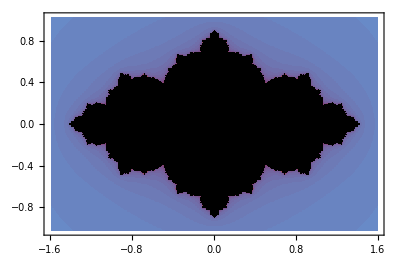
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
JuliaSetPlot/@Range[-1,1,0.1]
```

```mathematica
Table[JuliaSetPlot[RandomComplex[]],20]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
JuliaFractalDimension[c_]:=1+Abs[c]^2/4 Log[2]
```

```mathematica
MandelbrotSetPlot[]
```

-Graphics-

#### Sources

http://mathworld.wolfram.com/JuliaSet.html